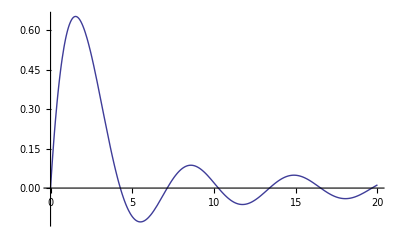

```mathematica
dom=20;
resan=DSolve[{y'[x]==-y[x]+1/x Sin[x],y[0]==0},y[x],x][[1,1,2]];
anplot=Plot[resan,{x,0,dom},PlotStyle->Thick]
```

```mathematica
h=0.01;
f=-y+1/x Sin[x];
k1=h f/.{x->xn,y->yn};
k2=h f/.{x->xn+0.5h,y->yn+0.5k1};
k3=h f/.{x->xn+0.5h,y->yn+0.5k2};
k4=h f/.{x->xn+h,y->yn+k3};
ynp1=yn+1/6 k1+1/3 k2+1/3 k3+1/6 k4
```

yn+0.00166667 (-yn+Sin[xn]/xn)+0.00333333 (-yn-0.005 (-yn+Sin[xn]/xn)+Sin[0.005+xn]/(0.005+xn))+0.00333333 (-yn+Sin[0.005+xn]/(0.005+xn)-0.005 (-yn-0.005 (-yn+Sin[xn]/xn)+Sin[0.005+xn]/(0.005+xn)))+0.00166667 (-yn-0.01 (-yn+Sin[0.005+xn]/(0.005+xn)-0.005 (-yn-0.005 (-yn+Sin[xn]/xn)+Sin[0.005+xn]/(0.005+xn)))+Sin[0.01+xn]/(0.01+xn))

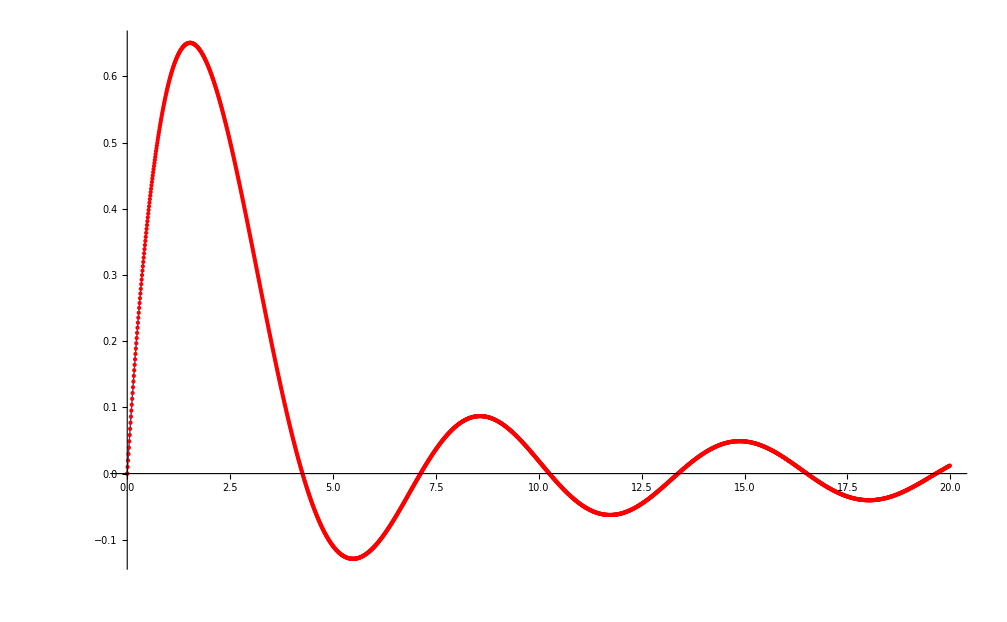

```mathematica
niter=dom/h+1;
yvec=Table[{0,0},{i,niter}];
xp=0;
yp=0;
For[i=2,i<niter,i++,
xp+=h;
yvec[[i,1]]=xp;
ynum=ynp1/.{xn->xp,yn->yp};
yvec[[i,2]]=ynum;
yp=yvec[[i,2]];
]
sol=ListPlot[yvec,PlotRange->All,PlotStyle->Red];
Show[anplot,sol]
```

# Caso 2

{{p[x]→(0.813099+1.84014×10^-15 ⅈ) ((1.+0. ⅈ) ⅇ^(0.05 x) Cos[0.998749 x]+(0.0122986+9.4901×10^-17 ⅈ) Cos[0.998749 x]^2+(0.122986-7.37762×10^-17 ⅈ) x Cos[0.998749 x]^2-(0.173203-8.35334×10^-17 ⅈ) ⅇ^(0.05 x) Sin[0.998749 x]+(5.12033×10^-17-6.57179×10^-17 ⅈ) Cos[0.998749 x] Sin[0.998749 x]-(8.19253×10^-16-7.50897×10^-17 ⅈ) x Cos[0.998749 x] Sin[0.998749 x]+(0.0122986+1.19091×10^-16 ⅈ) Sin[0.998749 x]^2+(0.122986+6.68675×10^-17 ⅈ) x Sin[0.998749 x]^2),Q[x]→(-0.1-1.1352×10^-16 ⅈ) ((1.+0. ⅈ) ⅇ^(0.05 x) Cos[0.998749 x]-(1.+0. ⅈ) Cos[0.998749 x]^2-(10.-1.06859×10^-14 ⅈ) x Cos[0.998749 x]^2+(8.19123+9.13324×10^-15 ⅈ) ⅇ^(0.05 x) Sin[0.998749 x]-(3.98986×10^-15+1.11301×10^-16 ⅈ) Cos[0.998749 x] Sin[0.998749 x]-(2.77556×10^-16+5.88462×10^-16 ⅈ) x Cos[0.998749 x] Sin[0.998749 x]-(1.+5.29379×10^-16 ⅈ) Sin[0.998749 x]^2-(10.-1.13799×10^-14 ⅈ) x Sin[0.998749 x]^2)}}

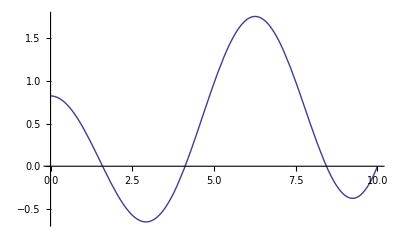

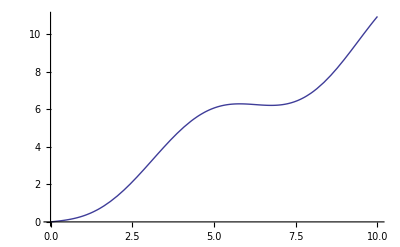

0.823099

```mathematica
dom=10;
res=DSolve[{Q'[x]==1-p[x]+0.1Q[x],p'[x]== Q[x]-x,Q[0]==0,p[dom]==0}, {Q[x],p[x]},x]
pf=res[[1,1,2]];
qf=res[[1,2,2]];
anpplot=Plot[pf,{x,0,dom},PlotRange->All,PlotStyle->Thick]
anqplot=Plot[qf,{x,0,dom},PlotRange->All,PlotStyle->Thick]
pini=pf/.x->0//N//Chop
```

## Runge-Kutta

```mathematica
h=0.01;
g=1-p+0.1 q;
f=q-x;
k1=h f/.{x->xn,p->pn,q->qn};
l1=h g/.{x->xn,p->pn,q->qn};
k2=h f/.{x->xn+0.5h,p->pn+0.5k1,q->qn+0.5l1};
l2=h g/.{x->xn+0.5h,p->pn+0.5k1,q->qn+0.5l1};
k3=h f/.{x->xn+0.5h,p->pn+0.5k2,q->qn+0.5l2};
l3=h g/.{x->xn+0.5h,p->pn+0.5k2,q->qn+0.5l2};
k4=h f/.{x->xn+h,p->pn+k3,q->qn+l3};
l4=h g/.{x->xn+h,p->pn+k3,q->qn+l3};

pnp1=pn+1/6 k1+1/3 k2+1/3 k3+1/6 k4;
qnp1=qn+1/6 l1+1/3 l2+1/3 l3+1/6 l4;
```

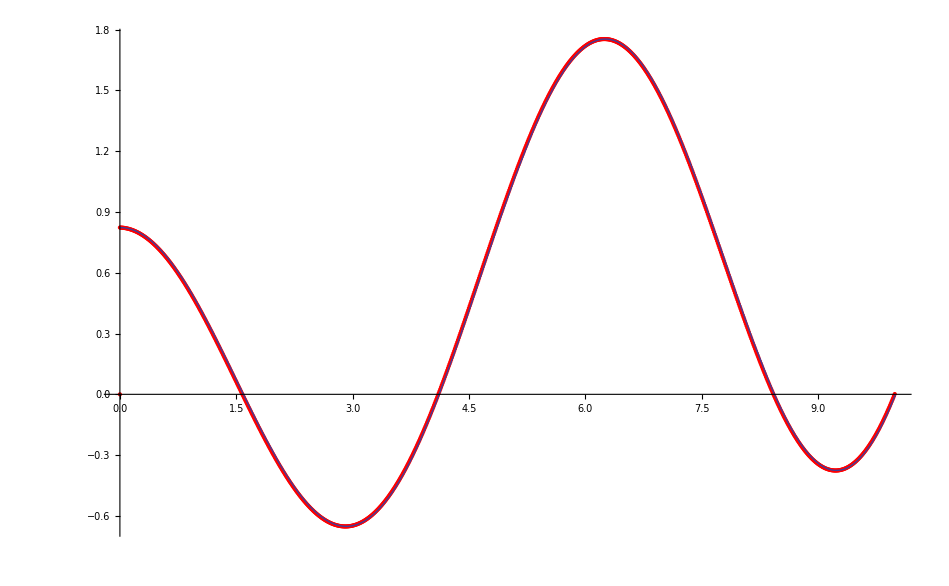

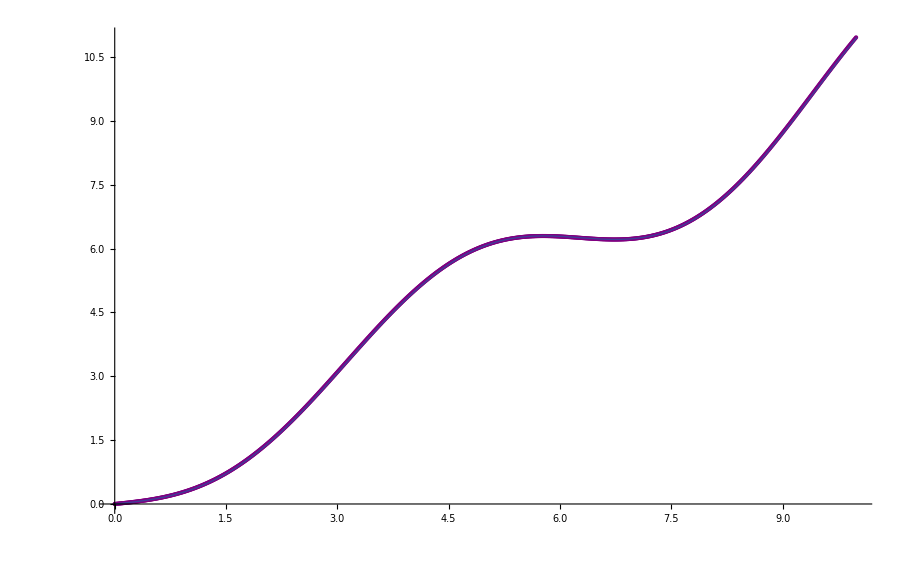

```mathematica
niter=dom/h+1;
pvec=Table[{0,0},{i,niter}];
qvec=Table[{0,0},{i,niter}];
pp=pini;
qp=0;
xp=0;
pvec[[1,2]]=pp;
qvec[[1,2]]=0;
For[i=2,i<niter,i++,
xp+=h;
pvec[[i,1]]=xp;
qvec[[i,1]]=xp;
pnum=pnp1/.{xn->xp,pn->pp,qn->qp};
qnum=qnp1/.{xn->xp,pn->pp,qn->qp};
pvec[[i,2]]=pnum;
qvec[[i,2]]=qnum;
pp=pnum;
qp=qnum;
]
solp=ListPlot[pvec,PlotRange->All,PlotStyle->Red];
solq=ListPlot[qvec,PlotRange->All,PlotStyle->Purple];
Show[solp,anpplot]
Show[solq,anqplot]
```

## Caso Simulado

```mathematica
μ=10^-8;
dt=1.;
lfrac=1000;
dom=lfrac;
hf=50000;
ν=0.2;
Ela=10^4;
Q=100;
G=Ela/(2(1+ν))
w=0.817(1-ν)hf p / G
pini=0.01;
wini=w/.p->pini
```

4166.67

7.8432 p

0.078432

## Runge-Kutta

```mathematica
h=-0.25;
g=wini/dt-w/dt;
f=-(12μ)/w^3 q;
k1=h f/.{x->xn,p->pn,q->qn};
l1=h g/.{x->xn,p->pn,q->qn};
k2=h f/.{x->xn+0.5h,p->pn+0.5k1,q->qn+0.5l1};
l2=h g/.{x->xn+0.5h,p->pn+0.5k1,q->qn+0.5l1};
k3=h f/.{x->xn+0.5h,p->pn+0.5k2,q->qn+0.5l2};
l3=h g/.{x->xn+0.5h,p->pn+0.5k2,q->qn+0.5l2};
k4=h f/.{x->xn+h,p->pn+k3,q->qn+l3};
l4=h g/.{x->xn+h,p->pn+k3,q->qn+l3};

pnp1=pn+1/6 k1+1/3 k2+1/3 k3+1/6 k4;
qnp1=qn+1/6 l1+1/3 l2+1/3 l3+1/6 l4;
```

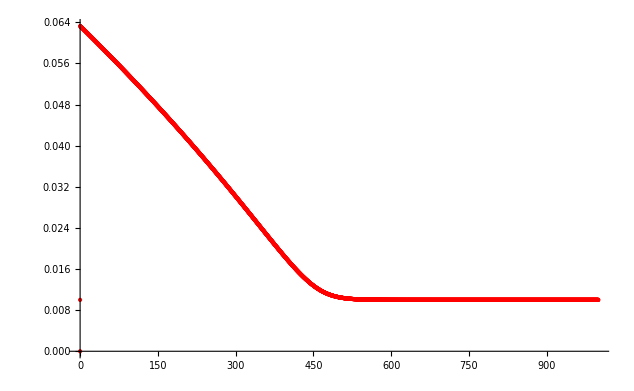

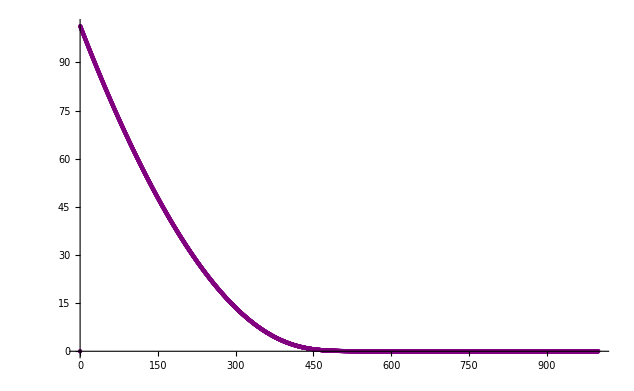

```mathematica
niter=dom/Abs[h]+1;
pvec=Table[{0,0},{i,niter}];
qvec=Table[{0,0},{i,niter}];
pp=0.01;
qp=5 10^-11;
xp=dom;
pvec[[1,2]]=pp;
qvec[[1,2]]=0;
For[i=2,i<niter,i++,
xp+=h;
pvec[[i,1]]=xp;
qvec[[i,1]]=xp;
pnum=pnp1/.{xn->xp,pn->pp,qn->qp};
qnum=qnp1/.{xn->xp,pn->pp,qn->qp};
pvec[[i,2]]=pnum;
qvec[[i,2]]=qnum;
pp=pnum;
qp=qnum;
]
solp=ListPlot[pvec,PlotRange->All,PlotStyle->Red];
solq=ListPlot[qvec,PlotRange->All,PlotStyle->Purple];
Show[solp]
Show[solq]
```